```mathematica
(* Defects with the symmetry along <100> direction *)
```

```mathematica
d100 = {1, 0, 0}; d010 = {0, 1, 0}; d001 = {0, 0, 1};
```

```mathematica
(* Defects with the symmetry along <110> direction *)
d110 = 1/√2*{1, 1, 0}; d101 = 1/√2*{1, 0, 1};
d011 = 1/√2*{0, 1, 1}; d1m10 = 1/√2*{1, -1, 0}; d01m1 = 1/√2*{0, 1, -1}; d10m1 = 1/√2*{1, 0, -1};
```

```mathematica
(* Defects with the symmetry along <111> direction *)
d111 = 1/√3*{1, 1, 1}; dm1m11 = 1/√3*{-1, -1, 1};
d1m1m1 = 1/√3*{1, -1, -1}; dm11m1 = 1/√3*{-1, 1, -1};
```

```mathematica
(* Rotation of the vector "d" in the XY plane by the angle theta "th" *)
Rot[d_, th_] := {d[[1]]*Cos[Pi*th/180]-d[[2]]*Sin[Pi*th/180], d[[1]]*Sin[Pi*th/180]+d[[2]]*Cos[Pi*th/180], d[[3]]};
```

```mathematica
(* Project vector b on a: Return part of b that is parallel to a *)
ParA[a_, b_] := a*(a.b)/Norm[a]^2;
(* Project vector b perpendicular to a: Return part of b that is orthogonal to a *)
PerpA[a_, b_] := b - ParA[a, b];
```

```mathematica
(* Orientations of the analyzer and laser field: co and cross*)
Lco = {0, 1, 0}; Lcr = {1, 0, 0};
```

```mathematica
(* NO Saturation: linear response*)
Lin[g_] := g;
```

```mathematica
(* YES Saturation with Gaussian beam *)
Sat[g_] := Log[1+g];
```

```mathematica
(* Determines which absorption function (linear L or saturated S) to use *)
absF[x_, sat_] := If[sat=="L", Lin[x], If[sat=="S", Sat[x], 0]];
```

```mathematica
(* Effective absorption amplitude. Electric Dipole and Magnetic Dipole absorption *)
```

```mathematica
PEabs[d_, L_, mAbs_, g_, sat_, th_] := If[mAbs=="z", absF[g*Norm[ParA[Rot[d, th], L]]^2, sat],If[mAbs=="xy",  absF[g*Norm[PerpA[Rot[d, th], L]]^2, sat], 0]];
PMabs[k_, d_, L_, mAbs_, g_, sat_, th_] := If[mAbs=="z", absF[g*Norm[ParA[Rot[d, th], Cross[k,L]]]^2, sat],If[mAbs=="xy",  absF[g*Norm[PerpA[Rot[d, th], Cross[k,L]]]^2, sat], 0]];
```

```mathematica
(* Effective absorption amplitude. Not perfectly anisotropic Electric Dipole moment *)
PabsB[d_, L_, mAbs_, g_, sat_, th_, B_] := If[mAbs=="z", absF[g*Norm[ParA[Rot[d, th], L]]^2*(1-B)+B, sat],If[mAbs=="xy",  absF[g*Norm[PerpA[Rot[d, th], L]]^2+B*g*Norm[ParA[Rot[d, th], L]]^2*(1-B)+B, sat], 0]];
```

```mathematica
(* Electric Dipole Z-type emission. Aperture Accounted for *)
```

```mathematica
Iz[d_, xM_] := 1/960 π (128 (d[[1]]^2+8 d[[2]]^2+d[[3]]^2)-30 (5d[[1]]^2+31 d[[2]]^2+4d[[3]]^2) Cos[xM]+5 (5 d[[1]]^2-17 d[[2]]^2-4d[[3]]^2) Cos[3 xM]-3 (d[[1]]^2+3 d[[2]]^2-4 d[[3]]^2) Cos[5 xM]);
```

```mathematica
(* Electric Dipole XY-type emission. Aperture Accounted for*)
```

```mathematica
Ixy[d_, xM_] := -1/12 π (-16+15 Cos[xM]+Cos[3 xM])-1/960 π (128 (d[[1]]^2+8 d[[2]]^2+d[[3]]^2)-30 (5d[[1]]^2+31 d[[2]]^2+4d[[3]]^2) Cos[xM]+5 (5 d[[1]]^2-17 d[[2]]^2-4d[[3]]^2) Cos[3 xM]-3 (d[[1]]^2+3 d[[2]]^2-4 d[[3]]^2) Cos[5 xM]);
```

```mathematica
(* Effective emission amplitude. We consider two cases: *)
(* E -- electric dipole and M -- magnetic dipole *)
(* For either of them dipole (p or m) can be parallel ("z") or *)
(* or perpendicular ("xy") to the defect vector *)
(* Electric dipole emission function *)
PEem[n_, d_, A_,  mEm_, th_] := If[mEm=="z", Norm[ParA[Rot[d, th], PerpA[n, A]]]^2, If[mEm=="xy",Norm[PerpA[Rot[d, th], PerpA[n, A]]]^2,0]];
PEemB[n_, d_, A_,  mEm_, th_, B_] := If[mEm=="z", Norm[ParA[Rot[d, th], PerpA[n, A]]]^2*(1-B)+B, If[mEm=="xy",Norm[PerpA[Rot[d, th], PerpA[n, A]]]^2*(1-B)+B,0]];
PEemAp[d_, mEm_, th_, xM_] := If[mEm=="z", Iz[Rot[d, th], xM], If[mEm=="xy",Ixy[Rot[d, th], xM],0]];
PMem[n_, d_, A_,  mEm_, th_] := If[mEm=="z", Norm[ParA[Rot[d, th], Cross[n, A]]]^2, If[mEm=="xy",Norm[PerpA[Rot[d, th], Cross[n, A]]]^2,0]];
```

```mathematica
PB[n_, d_, A_, L_, mAbs_, mEm_, g_, sat_, th_, B_] := PabsB[d, L, mAbs, g, sat, th, B]*PEemB[n, d,  A, mEm, th, B];
(*-------ED and MD functions; NOTE: k vector is ingored for E absorption----------*)
PE[k_, n_, d_, A_, L_, mAbs_, mEm_, g_, sat_, th_] := PEabs[d, L, mAbs, g, sat, th]*PEem[n, d, A, mEm, th];
PM[k_, n_, d_, A_, L_, mAbs_, mEm_, g_, sat_, th_] := PMabs[k, d, L, mAbs, g, sat, th]*PMem[n, d, A, mEm, th];
```

```mathematica
(* ED absorption-emission *)
PE100[A_, L_, mAbs_, mEm_, g_, sat_, th_ ] := PE[k, n, d100, A, L, mAbs, mEm, g, sat, th]+PE[k, n, d010, A, L, mAbs, mEm, g, sat, th]+PE[k, n, d001, A, L, mAbs, mEm, g, sat, th];
PE110[A_, L_, mAbs_, mEm_, g_, sat_, th_] := PE[k, n, d110, A, L, mAbs, mEm, g, sat, th]+PE[k, n, d101, A, L, mAbs, mEm, g, sat, th]+PE[k, n,d011, A, L, mAbs, mEm, g, sat, th]+PE[k, n, d1m10, A, L, mAbs, mEm, g, sat, th]+PE[k, d01m1, A, L, mAbs, mEm, g, sat, th]+PE[k,d10m1, A, L, mAbs, mEm, g, sat, th];
PE111[A_, L_, mAbs_, mEm_, g_, sat_, th_] := PE[k, n,d111, A, L, mAbs, mEm, g, sat, th]+PE[k, n, dm1m11, A, L, mAbs, mEm, g, sat, th]+PE[k,n, d1m1m1, A, L, mAbs, mEm, g, sat, th]+PE[k,n, dm11m1, A, L, mAbs, mEm, g, sat, th];
```

```mathematica
(* MD absorption-emission *)
PM100[A_, L_, mAbs_, mEm_, g_, sat_, th_ ] := PM[k, n, d100, A, L, mAbs, mEm, g, sat, th]+PM[k, n, d010, A, L, mAbs, mEm, g, sat, th]+PM[k, n, d001, A, L, mAbs, mEm, g, sat, th];
PM110[A_, L_, mAbs_, mEm_, g_, sat_, th_] := PM[k, n, d110, A, L, mAbs, mEm, g, sat, th]+PM[k, n, d101, A, L, mAbs, mEm, g, sat, th]+PM[k, n,d011, A, L, mAbs, mEm, g, sat, th]+PM[k, n, d1m10, A, L, mAbs, mEm, g, sat, th]+PM[k, d01m1, A, L, mAbs, mEm, g, sat, th]+PM[k,d10m1, A, L, mAbs, mEm, g, sat, th];
PM111[A_, L_, mAbs_, mEm_, g_, sat_, th_] := PM[k, n,d111, A, L, mAbs, mEm, g, sat, th]+PM[k, n, dm1m11, A, L, mAbs, mEm, g, sat, th]+PM[k,n, d1m1m1, A, L, mAbs, mEm, g, sat, th]+PM[k,n, dm11m1, A, L, mAbs, mEm, g, sat, th];
```

```mathematica
(*Checking Feofilov work: C3 in (100)+(110) orientation. Rotating Laser Polarization *)
```

```mathematica
k = 1/√2*{0, -1, -1}; fi = 45; k = {0, -Sin[ArcSin[1.5*Sin[Pi*fi/180]/2.42]], -Cos[ArcSin[1.5*Sin[Pi*fi/180]/2.42]]}; L1 = {1, 0, 0}; L2 = Cross[k, L1]; L = L1; A = L1;  n = -k;
```

```mathematica
Manipulate[Show[PolarPlot[PM111[A, L, "xy", "z", s, "S", 180*th/Pi], {th, 0, 2*Pi}, PlotStyle->{Red, Thick}], PolarPlot[PE111[A, L, "xy", "z", s, "S", 180*th/Pi], {th, 0, 2*Pi}, PlotStyle->{Blue, Thick}]],  {s, 8, 100}]
```

```mathematica
Manipulate[Show[Plot[PM111[A, L, "xy", "z", s, "S", th], {th, 0, 90}, PlotStyle->{Red, Thick}], Plot[PE111[A, L, "xy", "z", s, "S", th], {th, 0, 90}, PlotStyle->{Blue, Thick}]],  {s, 8, 100}]
```

```mathematica
Manipulate[Show[PolarPlot[PE111[A,L, "xy", "z", s, "L", 180*th/Pi], {th, 0, 2*Pi}, PlotStyle->{Blue, Thick}], PolarPlot[PE111[A, L, "z", "xy", s, "S", 180*th/Pi], {th, 0, 2*Pi}, PlotStyle->{Red, Thick}], PolarPlot[PE111[A, L, "xy", "z", s, "S", 180*th/Pi], {th, 0, 2*Pi}, PlotStyle->{Green, Thick}]], {s, 8, 500}]
```

```mathematica
Manipulate[Show[PolarPlot[PM111[A,L, "xy", "z", s, "L", 180*th/Pi], {th, 0, 2*Pi}, PlotStyle->{Blue, Thick}], PolarPlot[PM111[A, L, "z", "xy", s, "S", 180*th/Pi], {th, 0, 2*Pi}, PlotStyle->{Red, Thick}], PolarPlot[PM111[A, L, "xy", "z", s, "S", 180*th/Pi], {th, 0, 2*Pi}, PlotStyle->{Green, Thick}]], {s, 8, 500}]
```

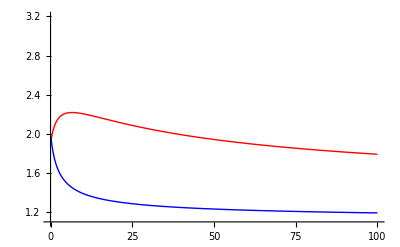

```mathematica
Show[Plot[PM111[A, L, "xy", "z", s, "S", 180*0/Pi]/PM111[A, L, "xy", "z", s, "S", 180*Pi/4/Pi], {s, 0.1, 100}, PlotStyle->{Red, Thick}, PlotRange->{{0, 100}, {1.1, 3.2}}], Plot[PE111[A, L, "xy", "z", s, "S", 180*0/Pi]/PE111[A, L, "xy", "z", s, "S", 180*Pi/4/Pi], {s, 0.1, 100}, PlotStyle->{Blue, Thick}, PlotRange->Full]]
```

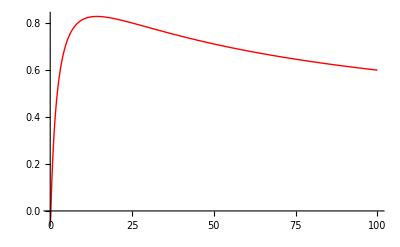

```mathematica
Plot[PM111[A, L, "xy", "z", s, "S", 180*0/Pi]/PM111[A, L, "xy", "z", s, "S", 180*Pi/4/Pi]-PE111[A, L, "xy", "z", s, "S", 180*0/Pi]/PE111[A, L, "xy", "z", s, "S", 180*Pi/4/Pi], {s, 0.1, 100}, PlotStyle->{Red, Thick}, PlotRange->Full](*{{0, 100}, {0.6, 1.2}}]*)
```

```mathematica
PolE111[mAbs_, mEm_, g_, sat_, th_] :=-( PE111[A1,Lx[th], mAbs, mEm, g, sat, 0]-PE111[A2,Lx[th], mAbs, mEm, g, sat, 0] )/ (PE111[A1,Lx[th], mAbs, mEm, g, sat, 0]+PE111[A2,Lx[th], mAbs, mEm, g, sat, 0] );
PolM111[mAbs_, mEm_, g_, sat_, th_] :=-( PM111[A1,Lx[th], mAbs, mEm, g, sat, 0]-PM111[A2,Lx[th], mAbs, mEm, g, sat, 0] )/ (PM111[A1,Lx[th], mAbs, mEm, g, sat, 0]+PM111[A2,Lx[th], mAbs, mEm, g, sat, 0] );
IE111[mAbs_, mEm_, g_, sat_, th_] := PE111[A1,Lx[th], mAbs, mEm, g, sat, 0]+ PE111[A2,Lx[th], mAbs, mEm, g, sat, 0];
IM111[mAbs_, mEm_, g_, sat_, th_] := PM111[A1,Lx[th], mAbs, mEm, g, sat, 0]+PM111[A2,Lx[th], mAbs, mEm, g, sat, 0] ;
```

```mathematica
Manipulate[Show[Plot[PolE111["z", "z", s, "L", th-Pi/4], {th, 0, Pi}, PlotStyle->{Blue, Thick}, PlotRange->Full], Plot[PolM111["z", "z", s, "L", th-Pi/4], {th, 0, Pi}, PlotStyle->{Red, Thick}, PlotRange->Full]], {s, 0.1, 50}]
```

Cross::nonn1: The arguments are expected to be vectors of equal length, and the number of arguments is expected to be 1 less than their length.

General::stop: Further output of Cross :: nonn1 will be suppressed during this calculation.

```mathematica
Manipulate[Show[Plot[IE111["z", "z", s, "L", th-Pi/4], {th, 0, Pi}, PlotStyle->{Blue, Thick}, PlotRange->Full], Plot[IM111["z", "z", s, "L", th-Pi/4], {th, 0, Pi}, PlotStyle->{Red, Thick}, PlotRange->Full]], {s, 0.1, 50}]
```

Cross::nonn1: The arguments are expected to be vectors of equal length, and the number of arguments is expected to be 1 less than their length.

General::stop: Further output of Cross :: nonn1 will be suppressed during this calculation.

```mathematica
Pol100[mAbs_, mEm_, g_, sat_, th_] :=( P100[A, Lco, mAbs, mEm, g, sat, th] - P100[A, Lcr, mAbs, mEm, g, sat, th] )/ ( P100[A, Lco, mAbs, mEm, g, sat, th] + P100[A, Lcr, mAbs, mEm, g, sat, th] );
```

```mathematica
Pol110[mAbs_, mEm_, g_, sat_, th_] :=( P110[A, Lco, mAbs, mEm, g, sat, th] - P110[A, Lcr, mAbs, mEm, g, sat, th] )/ ( P110[A, Lco, mAbs, mEm, g, sat, th] + P110[A, Lcr, mAbs, mEm, g, sat, th] );
```

```mathematica
Pol111[mAbs_, mEm_, g_, sat_, th_] :=( P111[A, Lco, mAbs, mEm, g, sat, th] - P111[A, Lcr, mAbs, mEm, g, sat, th] )/ ( P111[A, Lco, mAbs, mEm, g, sat, th] + P111[A, Lcr, mAbs, mEm, g, sat, th] );
```

```mathematica
Manipulate[Show[PolarPlot[Pol100["z", "z", s, "L",180*x/Pi], {x, 0, 2*Pi}, PlotStyle->{Blue, Thick}], PolarPlot[Pol100["z", "z", s, "S",180*x/Pi], {x, 0, 2*Pi}, PlotStyle->{Red, Thick}], PolarPlot[Pol100["z", "z", s, "S",180*x/Pi], {x, 0, 2*Pi}, PlotStyle->{Green, Thick}]], {s, 0.1, 50}]
```

```mathematica
Manipulate[Show[Plot[Pol111["z", "z", s, "L",180*x/Pi], {x, 0, 2*Pi}, PlotStyle->{Blue, Thick}], Plot[Pol111["z", "z", s, "S",180*x/Pi], {x, 0, 2*Pi}, PlotStyle->{Red, Thick}], Plot[Pol111["z", "z", s, "S",180*x/Pi], {x, 0, 2*Pi}, PlotStyle->{Green, Thick}]], {s, 0.1, 50}]
```

```mathematica
PlotSatPol100[abs_, em_] := Show[Plot[Pol100[abs, em, 10.0, "L",180*x/Pi], {x, 0, 2*Pi}, PlotStyle->{Blue, Thick}, PlotRange->All], Plot[Pol100[abs, em, 10.0, "S",180*x/Pi], {x, 0, 2*Pi}, PlotStyle->{Red, Thick}, PlotRange->All], Plot[Pol100[em, abs, 10.0, "S",180*x/Pi], {x, 0, 2*Pi}, PlotStyle->{Green, Thick, PlotRange->All}]];
```

```mathematica
PlotSatPol110[abs_, em_, s_] := Show[Plot[Pol110[abs, em, s, "L",180*x/Pi], {x, 0, 2*Pi}, PlotStyle->{Blue, Thick}, PlotRange->All], Plot[Pol110[abs, em, s, "S",180*x/Pi], {x, 0, 2*Pi}, PlotStyle->{Red, Thick}, PlotRange->All], Plot[Pol110[em, abs, s, "S",180*x/Pi], {x, 0, 2*Pi}, PlotStyle->{Green, Thick}, PlotRange->All]];
```

```mathematica
PlotSatPol111[abs_, em_, s_] := Show[Plot[Pol111[abs, em, s, "L",180*x/Pi], {x, 0, 2*Pi}, PlotStyle->{Blue, Thick}, PlotRange->All], Plot[Pol111[abs, em, s, "S",180*x/Pi], {x, 0, 2*Pi}, PlotStyle->{Red, Thick}, PlotRange->All], Plot[Pol111[em, abs, s, "S",180*x/Pi], {x, 0, 2*Pi}, PlotStyle->{Green, Thick}, PlotRange->All]];
```

```mathematica
PlotSatPol111["xy", "xy", 20]
```

-Graphics-

```mathematica
PlotSatPol111["xy", "xy", 100]
```

-Graphics-

```mathematica
Manipulate[ Show[Plot[Pol100["z", "z", 10.0, "L",180*th/Pi, B]/Pol100["z", "z", 10.0, "L",180*th/Pi, 0], {B, 0.0, 1.0}, PlotRange->Full], Plot[Pol110["z", "z", 10.0, "L",180*th/Pi, B]/Pol110["z", "z", 10.0, "L",180*th/Pi, 0], {B, 0.0, 1.0}, PlotRange->Full]], {th, 0, 90}]
```

```mathematica
Manipulate[Plot[Pol111["z", "z", 0.1, "L",180*th/Pi, B]/Pol111["z", "z", 0.1, "L",180*th/Pi, 0], {B, 0.0, 1.0}, PlotRange->Full], {th, 0.1, 90}]
```

```mathematica
H[b_] := (1-b)^2/( (1+b)^2+2*b^2);
```

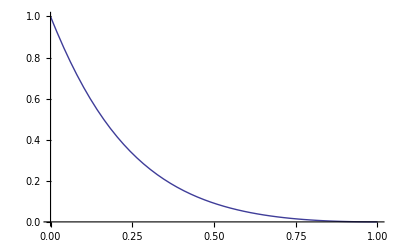

```mathematica
Plot[H[b], {b, 0, 1}]
```

```mathematica
Assuming[th >0 , FullSimplify[Expand[Pol100["z", "z", 1.0, "L",180*th/Pi, B]]]]/Assuming[th >0 , FullSimplify[Expand[Pol100["z", "z", 1.0, "L",180*th/Pi, 0]]]]
```

Pol100[z,z,1.,L,(180 th)/π,B]/Pol100[z,z,1.,L,(180 th)/π,0]

```mathematica
FullSimplify[Expand[Assuming[th >0 , FullSimplify[Expand[Pol100["z", "z", 1.0, "L",180*th/Pi, B]]]]/Assuming[th >0 , FullSimplify[Expand[Pol100["z", "z", 1.0, "L",180*th/Pi, 0]]]]]]
```

Pol100[z,z,1.,L,(180 th)/π,B]/Pol100[z,z,1.,L,(180 th)/π,0]

```mathematica
FullSimplify[Expand[Assuming[th >0  && B > 0, FullSimplify[Expand[Pol110["z", "z", 1.0, "L",180*th/Pi, B]]]]/Assuming[th >0 , FullSimplify[Expand[Pol110["z", "z", 1.0, "L",180*th/Pi, 0]]]]]]
```

Pol110[z,z,1.,L,(180 th)/π,B]/Pol110[z,z,1.,L,(180 th)/π,0]

```mathematica
(0.5-0.16666666666666669Cos[4 th])
```

0.5-0.166667 Cos[4 th]

```mathematica
(1.5+B (5+5.5 B))
```

1.5+B (5+5.5 B)

```mathematica
FullSimplify[Expand[Assuming[th >0  && B > 0, FullSimplify[Expand[Pol111["z", "z", 1.0, "L",180*th/Pi, B]]]]]]
```

Pol111[z,z,1.,L,(180 th)/π,B]